%%% Detremination of Axial ring down modes in pc - GR :
  %%% some default definition

```mathematica
Date[]
```

{2021,1,12,20,6,26.259556}

```mathematica
N[MachinePrecision,100]
```

15.95458977019100334632816142039813041871406371749175268945265543973673403154449900280714436226386712

%%% Number of iterations :

```mathematica
nmax=500;
```

%%% Take λ0 and s0 from Zerrili - equation - pcGR - axial modes :

```mathematica
λ0[xi_,ω_]:=-((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2);
s0[xi_,ω_]:=-((xi^3 (4800+19960 ω-20802 ω^2)+32 xi^6 (-3-10 ω+8 ω^2)-48 xi^5 (-16-57 ω+50 ω^2)-48 xi (-40-167 ω+96 ω^2)-36 (32+167 ω^2)+xi^4 (-2688-10216 ω+9817 ω^2)+xi^2 (-4416-20176 ω+21409 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2))
```

```mathematica
FF0:=Series[λ0[xi,ω],{xi,1/2,nmax}]
GG0:=Series[s0[xi,ω],{xi,1/2,nmax}]
```

Array[CC, {nmax + 1, nmax + 1}];
Array[DD, {nmax + 1, nmax + 1}];

```mathematica
For[i=1,i<(nmax+2), i++,
CC[i,1]=Coefficient[FF0,(xi-1/2),(i-1)];
DD[i,1]=Coefficient[GG0,(xi-1/2),(i-1)]]
```

```mathematica
For[i=1,i<(nmax+2), i++,
CC[i,1]=Simplify[CC[i,1]];
DD[i,1]=Simplify[DD[i,1]]]
```

%%% Set up of iteration equation, according to AIM

```mathematica
For[n=2,n<nmax+2,n++,
Print[n];
For[i=1,i<nmax+3-n,i++,
sumx=0;
sumy=0;
For[k=1,k<i+1,k++,
sumx=sumx+CC[k,1] CC[i-k+1,n-1];
sumy=sumy+DD[k,1] CC[i-k+1,n-1]
];
CC[i,n]=Expand[(i) CC[i+1,n-1]+DD[i,n-1]+sumx];
DD[i,n]=Expand[(i) DD[i+1,n-1]+sumy]
]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

%%%%   Only the coeffcients of zero orden in the Taylor serien of λ0 and s0

```mathematica
c0[n_]:=Expand[CC[1,n]]
d0[n_]:=Expand[DD[1,n]]
```

%%% Equations for convergence, AIM

```mathematica
δ[n_,ω_]:=d0[n]c0[n-1]-d0[n-1]c0[n]
```

%%% Define function to extract the roots :

```mathematica
raices[n_]:=N[Roots[δ[n,ω]==0,ω]]
```

%%%%       Calculation of the roots: %%
%%%%

```mathematica
R500=raices[500]
```

ω==0.00640139||ω==0.00676958||ω==0.0126685||ω==0.0158492||ω==0.0205161||ω==0.0281929||ω==0.0299931||ω==0.041114||ω==0.0438434||ω==0.0538928||ω==0.06283||ω==0.0683384||ω==0.0844512||ω==0.0852074||ω==0.102275||ω==0.111||ω==0.121799||ω==0.140299||ω==0.143054||ω==0.166039||ω==0.173207||ω==0.190807||ω==0.209792||ω==0.217371||ω==0.245729||ω==0.250219||ω==0.275972||ω==0.294557||ω==0.308087||ω==0.341992||ω==0.343116||ω==0.378055||ω==0.395708||ω==0.415993||ω==0.452813||ω==0.455935||ω==0.497914||ω==0.514529||ω==0.541968||ω==0.581007||ω==0.58819||ω==0.636312||ω==0.65265||ω==0.686776||ω==0.729198||ω==0.739412||ω==0.794265||ω==0.811639||ω==0.851364||ω==0.899808||ω==0.910722||ω==0.972389||ω==0.992828||ω==1.03621||ω==1.17271||ω==1.19903||ω==1.24287||ω==1.39632||ω==1.43141||ω==1.47311||ω==1.64317||ω==1.68924||ω==1.72719||ω==1.91355||ω==1.97108||ω==2.00385||ω==2.11532||ω==2.13515||ω==2.2071||ω==2.42001||ω==2.45991||ω==2.52361||ω==2.64343||ω==2.6572||ω==2.75304||ω==2.84526||ω==2.88401||ω==2.98772||ω==3.01612||ω==3.13243||ω==3.21796||ω==3.25768||ω==3.38874||ω==3.4537||ω==3.52063||ω==3.64479||ω==3.70633||ω==3.81253||ω==3.89821||ω==3.97948||ω==4.13379||ω==4.16132||ω==4.27029||ω==4.40991||ω==4.45155||ω==4.60358||ω==4.69295||ω==4.76008||ω==4.91057||ω==4.99205||ω==5.15059||ω==5.21674||ω==5.30863||ω==5.4832||ω==5.53175||ω==5.68954||ω==5.85838||ω==5.95639||ω==6.05945||ω==6.07872||ω==6.1282||ω==6.19576||ω==6.30598||ω==6.49789||ω==6.54508||ω==6.60041||ω==6.64926||ω==6.72108||ω==6.90391||ω==7.01837||ω==7.21389||ω==7.28026||ω==7.34195||ω==7.40801||ω==7.43985||ω==7.64769||ω==7.78393||ω==7.97429||ω==8.20083||ω==8.21093||ω==8.42672||ω==8.63021||ω==8.7833||ω==9.01511||ω==9.23076||ω==9.24426||ω==9.36937||ω==9.40676||ω==9.48168||ω==9.59963||ω==9.85911||ω==10.1279||ω==10.3107||ω==10.5542||ω==10.8482||ω==11.0173||ω==11.3372||ω==11.6079||ω==11.8426||ω==12.0993||ω==12.3607||ω==12.5952||ω==12.852||ω==13.1072||ω==13.3408||ω==13.6007||ω==13.8494||ω==14.0825||ω==14.3521||ω==14.5978||ω==14.8481||ω==15.1171||ω==15.3577||ω==15.6092||ω==15.8608||ω==16.0983||ω==16.3535||ω==16.6036||ω==16.8542||ω==17.1155||ω==17.3573||ω==17.6055||ω==17.8561||ω==18.1025||ω==18.3636||ω==18.6099||ω==18.8556||ω==19.1081||ω==19.3563||ω==19.6128||ω==19.8592||ω==20.105||ω==20.3615||ω==20.6099||ω==20.8604||ω==21.108||ω==21.3592||ω==21.6133||ω==21.8577||ω==22.11||ω==22.3622||ω==22.61||ω==22.8606||ω==23.1104||ω==23.3625||ω==23.6097||ω==23.8611||ω==24.1131||ω==24.3594||ω==24.6127||ω==24.862||ω==25.1109||ω==25.3627||ω==25.6119||ω==25.8621||ω==26.1122||ω==26.3628||ω==26.6118||ω==26.863||ω==27.1127||ω==27.3621||ω==27.6138||ω==27.8619||ω==28.1137||ω==28.363||ω==28.6127||ω==28.8641||ω==29.1124||ω==29.3642||ω==29.6131||ω==29.8637||ω==30.114||ω==30.3632||ω==30.6145||ω==30.8633||ω==31.1145||ω==31.3638||ω==31.6142||ω==31.8643||ω==32.114||ω==32.3647||ω==32.6139||ω==32.8649||ω==33.1141||ω==33.3649||ω==33.6144||ω==33.8648||ω==34.1148||ω==34.3647||ω==34.6151||ω==34.8647||ω==35.1153||ω==35.3648||ω==35.6154||ω==35.865||ω==36.1155||ω==36.3652||ω==36.6155||ω==36.8653||ω==37.1155||ω==37.3655||ω==37.6156||ω==37.8656||ω==38.1157||ω==38.3657||ω==38.6158||ω==38.8658||ω==39.1159||ω==39.3658||ω==39.6161||ω==39.8659||ω==40.1161||ω==40.366||ω==40.6162||ω==40.8662||ω==41.1162||ω==41.3663||ω==41.6163||ω==41.8664||ω==42.1164||ω==42.3665||ω==42.6164||ω==42.8666||ω==43.1165||ω==43.3666||ω==43.6166||ω==43.8667||ω==44.1167||ω==44.3668||ω==44.6168||ω==44.8669||ω==45.1169||ω==45.3669||ω==45.6169||ω==45.867||ω==46.117||ω==46.3671||ω==46.6171||ω==46.8671||ω==47.1172||ω==47.3672||ω==47.6173||ω==47.8672||ω==48.1173||ω==48.3673||ω==48.6174||ω==48.8674||ω==49.1174||ω==49.3675||ω==49.6175||ω==49.8675||ω==50.1176||ω==50.3676||ω==50.6176||ω==50.8677||ω==51.1177||ω==51.3677||ω==51.6177||ω==51.8678||ω==52.1178||ω==52.3678||ω==52.6178||ω==52.8679||ω==53.1179||ω==53.3679||ω==53.6179||ω==53.868||ω==54.118||ω==54.368||ω==54.618||ω==54.8681||ω==55.1181||ω==55.3681||ω==55.6182||ω==55.8682||ω==56.1182||ω==56.3682||ω==56.6182||ω==56.8683||ω==57.1183||ω==57.3683||ω==57.6184||ω==57.8684||ω==58.1184||ω==58.3684||ω==58.6184||ω==58.8685||ω==59.1185||ω==59.3685||ω==59.6185||ω==59.8686||ω==60.1186||ω==60.3686||ω==60.6186||ω==60.8686||ω==61.1187||ω==61.3687||ω==61.6187||ω==61.8687||ω==62.1188||ω==62.3688||ω==62.6188||ω==62.8688||ω==63.1188||ω==63.3689||ω==63.6189||ω==63.8689||ω==64.1189||ω==64.3689||ω==64.619||ω==64.869||ω==65.119||ω==65.369||ω==65.619||ω==65.869||ω==66.1191||ω==66.3691||ω==66.6191||ω==66.8691||ω==67.1191||ω==67.3692||ω==67.6192||ω==67.8692||ω==68.1192||ω==68.3692||ω==68.6192||ω==68.8693||ω==69.1193||ω==69.3693||ω==69.6193||ω==69.8693||ω==70.1193||ω==70.3694||ω==70.6194||ω==70.8694||ω==71.1194||ω==71.3694||ω==71.6194||ω==71.8695||ω==72.1195||ω==72.3695||ω==72.6195||ω==72.8695||ω==73.1195||ω==73.3695||ω==73.6196||ω==73.8696||ω==74.1196||ω==74.3696||ω==74.6196||ω==74.8696||ω==75.1196||ω==75.3697||ω==75.6197||ω==75.8697||ω==76.1197||ω==76.3697||ω==76.6197||ω==76.8697||ω==77.1198||ω==77.3698||ω==77.6198||ω==77.8698||ω==78.1198||ω==78.3698||ω==78.6198||ω==78.8699||ω==79.1199||ω==79.3699||ω==79.6199||ω==79.8699||ω==80.1199||ω==80.3699||ω==80.6199||ω==80.87||ω==81.12||ω==81.37||ω==81.62||ω==81.87||ω==82.12||ω==82.37||ω==82.62||ω==82.8701||ω==83.1201||ω==83.3701||ω==83.6201||ω==83.8701||ω==84.1201||ω==84.3701||ω==84.6201||ω==84.8702||ω==85.1202||ω==85.3702||ω==85.6202||ω==85.8702||ω==86.1202||ω==86.3702||ω==86.6202||ω==86.8702||ω==87.1203||ω==87.3703||ω==87.6203||ω==87.8703||ω==88.1203||ω==88.3703||ω==88.6203||ω==88.8703||ω==89.1203||ω==89.3704||ω==89.6204||ω==89.8704||ω==90.1204||ω==90.3704||ω==90.6204||ω==90.8704||ω==91.1204||ω==91.3704||ω==91.6204||ω==91.8705||ω==92.1205||ω==92.3705||ω==92.6205||ω==92.8705||ω==93.1205||ω==93.3705||ω==93.6205||ω==93.8705||ω==94.1205||ω==94.3706||ω==94.6206||ω==94.8706||ω==95.1206||ω==95.3706||ω==95.6206||ω==95.8706||ω==96.1206||ω==96.3706||ω==96.6206||ω==96.8706||ω==97.1207||ω==97.3707||ω==97.6207||ω==97.8705||ω==98.1205||ω==98.3707||ω==98.6204||ω==98.8731||ω==99.1297||ω==99.3746||ω==99.6278||ω==99.8338||ω==99.9724||ω==100.314||ω==100.626||ω==100.869||ω==101.252||ω==101.637||ω==101.879||ω==102.221||ω==102.63||ω==102.916||ω==103.207||ω==103.622||ω==103.96||ω==104.215||ω==104.625||ω==105.003||ω==105.245||ω==105.642||ω==106.047||ω==106.293||ω==106.676||ω==107.099||ω==107.353||ω==107.73||ω==108.165||ω==108.423||ω==108.806||ω==109.246||ω==109.502||ω==109.905||ω==110.344||ω==110.596||ω==111.034||ω==111.451||ω==111.715||ω==112.196||ω==112.557||ω==112.879||ω==113.387||ω==113.669||ω==114.108||ω==114.571||ω==114.85||ω==115.404||ω==115.707||ω==116.182||ω==116.643||ω==116.981||ω==117.576||ω==117.841||ω==118.506||ω==118.779||ω==119.517||ω==119.787||ω==120.669||ω==121.635||ω==122.611||ω==123.593||ω==124.58||ω==125.576||ω==126.58||ω==127.595||ω==128.622||ω==129.664||ω==130.722||ω==131.797||ω==132.893||ω==134.011||ω==135.154||ω==136.325||ω==137.527||ω==138.764||ω==140.022||ω==141.631||ω==141.969||ω==0.078206-0.388691 ⅈ||ω==0.078206+0.388691 ⅈ||ω==0.23905-0.361323 ⅈ||ω==0.23905+0.361323 ⅈ||ω==0.414656-0.309183 ⅈ||ω==0.414656+0.309183 ⅈ||ω==0.615588-0.243026 ⅈ||ω==0.615588+0.243026 ⅈ||ω==0.841467-0.18132 ⅈ||ω==0.841467+0.18132 ⅈ||ω==1.08048-0.134408 ⅈ||ω==1.08048+0.134408 ⅈ||ω==1.0987-0.0021909 ⅈ||ω==1.0987+0.0021909 ⅈ||ω==1.31489-0.00884982 ⅈ||ω==1.31489+0.00884982 ⅈ||ω==1.32438-0.101762 ⅈ||ω==1.32438+0.101762 ⅈ||ω==1.55554-0.0127988 ⅈ||ω==1.55554+0.0127988 ⅈ||ω==1.57112-0.079542 ⅈ||ω==1.57112+0.079542 ⅈ||ω==1.81715-0.0632229 ⅈ||ω==1.81715+0.0632229 ⅈ||ω==1.82646-0.0154759 ⅈ||ω==1.82646+0.0154759 ⅈ||ω==2.06617-0.0601996 ⅈ||ω==2.06617+0.0601996 ⅈ||ω==2.29124-0.0123922 ⅈ||ω==2.29124+0.0123922 ⅈ||ω==2.32894-0.0480465 ⅈ||ω==2.32894+0.0480465 ⅈ||ω==2.56917-0.0514434 ⅈ||ω==2.56917+0.0514434 ⅈ||ω==2.8158-0.0326914 ⅈ||ω==2.8158+0.0326914 ⅈ||ω==3.08235-0.0423122 ⅈ||ω==3.08235+0.0423122 ⅈ||ω==3.32973-0.0452338 ⅈ||ω==3.32973+0.0452338 ⅈ||ω==3.58012-0.0407552 ⅈ||ω==3.58012+0.0407552 ⅈ||ω==3.82694-0.019517 ⅈ||ω==3.82694+0.019517 ⅈ||ω==4.06596-0.0355869 ⅈ||ω==4.06596+0.0355869 ⅈ||ω==4.32643-0.0367557 ⅈ||ω==4.32643+0.0367557 ⅈ||ω==4.57438-0.034719 ⅈ||ω==4.57438+0.034719 ⅈ||ω==4.84067-0.0380216 ⅈ||ω==4.84067+0.0380216 ⅈ||ω==5.07886-0.0363821 ⅈ||ω==5.07886+0.0363821 ⅈ||ω==5.3546-0.0390055 ⅈ||ω==5.3546+0.0390055 ⅈ||ω==5.6112-0.0195368 ⅈ||ω==5.6112+0.0195368 ⅈ||ω==5.82555-0.027245 ⅈ||ω==5.82555+0.027245 ⅈ||ω==6.35639-0.0405743 ⅈ||ω==6.35639+0.0405743 ⅈ||ω==6.84505-0.0365676 ⅈ||ω==6.84505+0.0365676 ⅈ||ω==7.09309-0.041231 ⅈ||ω==7.09309+0.041231 ⅈ||ω==7.59626-0.0396596 ⅈ||ω==7.59626+0.0396596 ⅈ||ω==7.84509-0.0348128 ⅈ||ω==7.84509+0.0348128 ⅈ||ω==8.06921-0.0222 ⅈ||ω==8.06921+0.0222 ⅈ||ω==8.36832-0.0305545 ⅈ||ω==8.36832+0.0305545 ⅈ||ω==8.59691-0.0342992 ⅈ||ω==8.59691+0.0342992 ⅈ||ω==8.84838-0.0449557 ⅈ||ω==8.84838+0.0449557 ⅈ||ω==9.07081-0.00796216 ⅈ||ω==9.07081+0.00796216 ⅈ||ω==9.66583-0.0254297 ⅈ||ω==9.66583+0.0254297 ⅈ||ω==9.88305-0.0386534 ⅈ||ω==9.88305+0.0386534 ⅈ||ω==10.0995-0.0442933 ⅈ||ω==10.0995+0.0442933 ⅈ||ω==10.3547-0.0473737 ⅈ||ω==10.3547+0.0473737 ⅈ||ω==10.5869-0.0444019 ⅈ||ω==10.5869+0.0444019 ⅈ||ω==10.7988-0.0374378 ⅈ||ω==10.7988+0.0374378 ⅈ||ω==11.0681-0.0236093 ⅈ||ω==11.0681+0.0236093 ⅈ||ω==11.2708-0.0295894 ⅈ||ω==11.2708+0.0295894 ⅈ||ω==11.503-0.0421701 ⅈ||ω==11.503+0.0421701 ⅈ||ω==11.746-0.0267048 ⅈ||ω==11.746+0.0267048 ⅈ||ω==11.9902-0.0434462 ⅈ||ω==11.9902+0.0434462 ⅈ||ω==12.2348-0.0500304 ⅈ||ω==12.2348+0.0500304 ⅈ||ω==12.486-0.0407777 ⅈ||ω==12.486+0.0407777 ⅈ||ω==12.7399-0.0544811 ⅈ||ω==12.7399+0.0544811 ⅈ||ω==12.9941-0.0577023 ⅈ||ω==12.9941+0.0577023 ⅈ||ω==13.2565-0.0526962 ⅈ||ω==13.2565+0.0526962 ⅈ||ω==13.5171-0.0652266 ⅈ||ω==13.5171+0.0652266 ⅈ||ω==13.7817-0.0667026 ⅈ||ω==13.7817+0.0667026 ⅈ||ω==14.0553-0.0691099 ⅈ||ω==14.0553+0.0691099 ⅈ||ω==14.3191-0.0788082 ⅈ||ω==14.3191+0.0788082 ⅈ||ω==14.5933-0.0813861 ⅈ||ω==14.5933+0.0813861 ⅈ||ω==14.8687-0.0871437 ⅈ||ω==14.8687+0.0871437 ⅈ||ω==15.1413-0.087179 ⅈ||ω==15.1413+0.087179 ⅈ||ω==15.4264-0.0897076 ⅈ||ω==15.4264+0.0897076 ⅈ||ω==15.7114-0.0920591 ⅈ||ω==15.7114+0.0920591 ⅈ||ω==16.0026-0.0920594 ⅈ||ω==16.0026+0.0920594 ⅈ||ω==16.2945-0.100325 ⅈ||ω==16.2945+0.100325 ⅈ||ω==16.5885-0.104688 ⅈ||ω==16.5885+0.104688 ⅈ||ω==16.8851-0.109804 ⅈ||ω==16.8851+0.109804 ⅈ||ω==17.183-0.110063 ⅈ||ω==17.183+0.110063 ⅈ||ω==17.4895-0.11401 ⅈ||ω==17.4895+0.11401 ⅈ||ω==17.797-0.118977 ⅈ||ω==17.797+0.118977 ⅈ||ω==18.1078-0.124446 ⅈ||ω==18.1078+0.124446 ⅈ||ω==18.418-0.12739 ⅈ||ω==18.418+0.12739 ⅈ||ω==18.7364-0.130414 ⅈ||ω==18.7364+0.130414 ⅈ||ω==19.0565-0.13611 ⅈ||ω==19.0565+0.13611 ⅈ||ω==19.3795-0.141133 ⅈ||ω==19.3795+0.141133 ⅈ||ω==19.7046-0.144192 ⅈ||ω==19.7046+0.144192 ⅈ||ω==20.0361-0.1488 ⅈ||ω==20.0361+0.1488 ⅈ||ω==20.3678-0.154487 ⅈ||ω==20.3678+0.154487 ⅈ||ω==20.7043-0.158647 ⅈ||ω==20.7043+0.158647 ⅈ||ω==21.0447-0.163294 ⅈ||ω==21.0447+0.163294 ⅈ||ω==21.3875-0.169032 ⅈ||ω==21.3875+0.169032 ⅈ||ω==21.734-0.17288 ⅈ||ω==21.734+0.17288 ⅈ||ω==22.0843-0.179015 ⅈ||ω==22.0843+0.179015 ⅈ||ω==22.4375-0.183779 ⅈ||ω==22.4375+0.183779 ⅈ||ω==22.7949-0.189305 ⅈ||ω==22.7949+0.189305 ⅈ||ω==23.1554-0.194937 ⅈ||ω==23.1554+0.194937 ⅈ||ω==23.5197-0.200064 ⅈ||ω==23.5197+0.200064 ⅈ||ω==23.8874-0.206206 ⅈ||ω==23.8874+0.206206 ⅈ||ω==24.2589-0.211521 ⅈ||ω==24.2589+0.211521 ⅈ||ω==24.6338-0.217801 ⅈ||ω==24.6338+0.217801 ⅈ||ω==25.0128-0.223633 ⅈ||ω==25.0128+0.223633 ⅈ||ω==25.3952-0.229881 ⅈ||ω==25.3952+0.229881 ⅈ||ω==25.7815-0.236118 ⅈ||ω==25.7815+0.236118 ⅈ||ω==26.1716-0.242545 ⅈ||ω==26.1716+0.242545 ⅈ||ω==26.5655-0.249007 ⅈ||ω==26.5655+0.249007 ⅈ||ω==26.9632-0.255661 ⅈ||ω==26.9632+0.255661 ⅈ||ω==27.365-0.262493 ⅈ||ω==27.365+0.262493 ⅈ||ω==27.7705-0.269297 ⅈ||ω==27.7705+0.269297 ⅈ||ω==28.18-0.276414 ⅈ||ω==28.18+0.276414 ⅈ||ω==28.5937-0.283624 ⅈ||ω==28.5937+0.283624 ⅈ||ω==29.0113-0.290888 ⅈ||ω==29.0113+0.290888 ⅈ||ω==29.433-0.298395 ⅈ||ω==29.433+0.298395 ⅈ||ω==29.8589-0.306053 ⅈ||ω==29.8589+0.306053 ⅈ||ω==30.289-0.313801 ⅈ||ω==30.289+0.313801 ⅈ||ω==30.7232-0.321718 ⅈ||ω==30.7232+0.321718 ⅈ||ω==31.1618-0.329826 ⅈ||ω==31.1618+0.329826 ⅈ||ω==31.6046-0.338086 ⅈ||ω==31.6046+0.338086 ⅈ||ω==32.0518-0.34649 ⅈ||ω==32.0518+0.34649 ⅈ||ω==32.5034-0.355062 ⅈ||ω==32.5034+0.355062 ⅈ||ω==32.9595-0.363815 ⅈ||ω==32.9595+0.363815 ⅈ||ω==33.4201-0.372749 ⅈ||ω==33.4201+0.372749 ⅈ||ω==33.8852-0.381859 ⅈ||ω==33.8852+0.381859 ⅈ||ω==34.355-0.391146 ⅈ||ω==34.355+0.391146 ⅈ||ω==34.8294-0.400619 ⅈ||ω==34.8294+0.400619 ⅈ||ω==35.3086-0.410282 ⅈ||ω==35.3086+0.410282 ⅈ||ω==35.7926-0.420143 ⅈ||ω==35.7926+0.420143 ⅈ||ω==36.2814-0.430203 ⅈ||ω==36.2814+0.430203 ⅈ||ω==36.7751-0.440468 ⅈ||ω==36.7751+0.440468 ⅈ||ω==37.2738-0.450941 ⅈ||ω==37.2738+0.450941 ⅈ||ω==37.7775-0.461627 ⅈ||ω==37.7775+0.461627 ⅈ||ω==38.2864-0.472531 ⅈ||ω==38.2864+0.472531 ⅈ||ω==38.8004-0.483659 ⅈ||ω==38.8004+0.483659 ⅈ||ω==39.3197-0.495016 ⅈ||ω==39.3197+0.495016 ⅈ||ω==39.8443-0.506608 ⅈ||ω==39.8443+0.506608 ⅈ||ω==40.3743-0.51844 ⅈ||ω==40.3743+0.51844 ⅈ||ω==40.9098-0.530518 ⅈ||ω==40.9098+0.530518 ⅈ||ω==41.4508-0.542849 ⅈ||ω==41.4508+0.542849 ⅈ||ω==41.9976-0.555439 ⅈ||ω==41.9976+0.555439 ⅈ||ω==42.55-0.568294 ⅈ||ω==42.55+0.568294 ⅈ||ω==43.1083-0.581422 ⅈ||ω==43.1083+0.581422 ⅈ||ω==43.6725-0.594829 ⅈ||ω==43.6725+0.594829 ⅈ||ω==44.2428-0.608523 ⅈ||ω==44.2428+0.608523 ⅈ||ω==44.8191-0.622511 ⅈ||ω==44.8191+0.622511 ⅈ||ω==45.4017-0.636803 ⅈ||ω==45.4017+0.636803 ⅈ||ω==45.9906-0.651405 ⅈ||ω==45.9906+0.651405 ⅈ||ω==46.586-0.666327 ⅈ||ω==46.586+0.666327 ⅈ||ω==47.188-0.681578 ⅈ||ω==47.188+0.681578 ⅈ||ω==47.7966-0.697167 ⅈ||ω==47.7966+0.697167 ⅈ||ω==48.412-0.713104 ⅈ||ω==48.412+0.713104 ⅈ||ω==49.0344-0.729399 ⅈ||ω==49.0344+0.729399 ⅈ||ω==49.6639-0.746064 ⅈ||ω==49.6639+0.746064 ⅈ||ω==50.3006-0.763108 ⅈ||ω==50.3006+0.763108 ⅈ||ω==50.9447-0.780544 ⅈ||ω==50.9447+0.780544 ⅈ||ω==51.5963-0.798384 ⅈ||ω==51.5963+0.798384 ⅈ||ω==52.2556-0.816641 ⅈ||ω==52.2556+0.816641 ⅈ||ω==52.9227-0.835328 ⅈ||ω==52.9227+0.835328 ⅈ||ω==53.5979-0.854459 ⅈ||ω==53.5979+0.854459 ⅈ||ω==54.2813-0.87405 ⅈ||ω==54.2813+0.87405 ⅈ||ω==54.9731-0.894115 ⅈ||ω==54.9731+0.894115 ⅈ||ω==55.6735-0.91467 ⅈ||ω==55.6735+0.91467 ⅈ||ω==56.3827-0.935734 ⅈ||ω==56.3827+0.935734 ⅈ||ω==57.101-0.957323 ⅈ||ω==57.101+0.957323 ⅈ||ω==57.8286-0.979457 ⅈ||ω==57.8286+0.979457 ⅈ||ω==58.5657-1.00216 ⅈ||ω==58.5657+1.00216 ⅈ||ω==59.3126-1.02544 ⅈ||ω==59.3126+1.02544 ⅈ||ω==60.0695-1.04934 ⅈ||ω==60.0695+1.04934 ⅈ||ω==60.8368-1.07386 ⅈ||ω==60.8368+1.07386 ⅈ||ω==61.6148-1.09904 ⅈ||ω==61.6148+1.09904 ⅈ||ω==62.4038-1.12491 ⅈ||ω==62.4038+1.12491 ⅈ||ω==63.204-1.15149 ⅈ||ω==63.204+1.15149 ⅈ||ω==64.016-1.17881 ⅈ||ω==64.016+1.17881 ⅈ||ω==64.8401-1.20691 ⅈ||ω==64.8401+1.20691 ⅈ||ω==65.6767-1.23581 ⅈ||ω==65.6767+1.23581 ⅈ||ω==66.5262-1.26556 ⅈ||ω==66.5262+1.26556 ⅈ||ω==67.3891-1.29619 ⅈ||ω==67.3891+1.29619 ⅈ||ω==68.266-1.32775 ⅈ||ω==68.266+1.32775 ⅈ||ω==69.1574-1.36028 ⅈ||ω==69.1574+1.36028 ⅈ||ω==70.0638-1.39382 ⅈ||ω==70.0638+1.39382 ⅈ||ω==70.9859-1.42844 ⅈ||ω==70.9859+1.42844 ⅈ||ω==71.9245-1.46419 ⅈ||ω==71.9245+1.46419 ⅈ||ω==72.8801-1.50112 ⅈ||ω==72.8801+1.50112 ⅈ||ω==73.8537-1.53931 ⅈ||ω==73.8537+1.53931 ⅈ||ω==74.8462-1.57883 ⅈ||ω==74.8462+1.57883 ⅈ||ω==75.8585-1.61975 ⅈ||ω==75.8585+1.61975 ⅈ||ω==76.8916-1.66216 ⅈ||ω==76.8916+1.66216 ⅈ||ω==77.9468-1.70616 ⅈ||ω==77.9468+1.70616 ⅈ||ω==79.0255-1.75185 ⅈ||ω==79.0255+1.75185 ⅈ||ω==80.1289-1.79934 ⅈ||ω==80.1289+1.79934 ⅈ||ω==81.2588-1.84877 ⅈ||ω==81.2588+1.84877 ⅈ||ω==82.4171-1.90028 ⅈ||ω==82.4171+1.90028 ⅈ||ω==83.6058-1.95403 ⅈ||ω==83.6058+1.95403 ⅈ||ω==84.8272-2.01021 ⅈ||ω==84.8272+2.01021 ⅈ||ω==86.0843-2.06901 ⅈ||ω==86.0843+2.06901 ⅈ||ω==87.3801-2.13068 ⅈ||ω==87.3801+2.13068 ⅈ||ω==88.7184-2.19549 ⅈ||ω==88.7184+2.19549 ⅈ||ω==90.1036-2.26377 ⅈ||ω==90.1036+2.26377 ⅈ||ω==91.5412-2.33589 ⅈ||ω==91.5412+2.33589 ⅈ||ω==93.0377-2.41231 ⅈ||ω==93.0377+2.41231 ⅈ||ω==94.6011-2.49358 ⅈ||ω==94.6011+2.49358 ⅈ||ω==96.242-2.58038 ⅈ||ω==96.242+2.58038 ⅈ||ω==97.9739-2.67357 ⅈ||ω==97.9739+2.67357 ⅈ||ω==99.8152-2.77438 ⅈ||ω==99.8152+2.77438 ⅈ||ω==100.784-0.942388 ⅈ||ω==100.784+0.942388 ⅈ||ω==101.808-2.90145 ⅈ||ω==101.808+2.90145 ⅈ||ω==101.838-2.03871 ⅈ||ω==101.838+2.03871 ⅈ||ω==103.053-2.94094 ⅈ||ω==103.053+2.94094 ⅈ||ω==103.845-3.48685 ⅈ||ω==103.845+3.48685 ⅈ||ω==104.763-3.85275 ⅈ||ω==104.763+3.85275 ⅈ||ω==105.712-4.30693 ⅈ||ω==105.712+4.30693 ⅈ||ω==106.668-4.73507 ⅈ||ω==106.668+4.73507 ⅈ||ω==107.671-5.16902 ⅈ||ω==107.671+5.16902 ⅈ||ω==108.705-5.60803 ⅈ||ω==108.705+5.60803 ⅈ||ω==109.784-6.04386 ⅈ||ω==109.784+6.04386 ⅈ||ω==110.918-6.48389 ⅈ||ω==110.918+6.48389 ⅈ||ω==112.117-6.92428 ⅈ||ω==112.117+6.92428 ⅈ||ω==113.406-7.36394 ⅈ||ω==113.406+7.36394 ⅈ||ω==114.818-7.80887 ⅈ||ω==114.818+7.80887 ⅈ||ω==116.411-8.2596 ⅈ||ω==116.411+8.2596 ⅈ||ω==118.356-8.70955 ⅈ||ω==118.356+8.70955 ⅈ||ω==144.114-1.65634 ⅈ||ω==144.114+1.65634 ⅈ

500

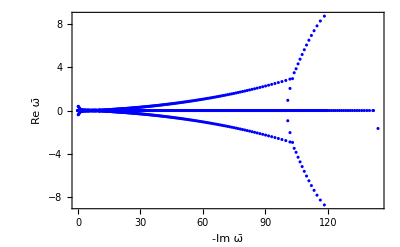

500 =n

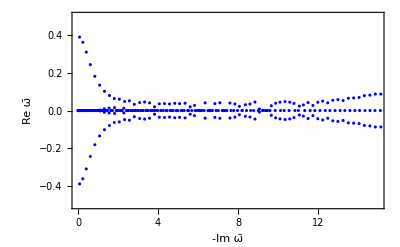

```mathematica
l500=Length[R500]-1;
d=(l500+1)/2
f500=ListPlot[
Table[{Re[R500[[k]][[2]]],Im[R500[[k]][[2]]]},{k,1,l500}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Blue]
Print[d"=n"]
h500=Show[f500,PlotRange -> {{0,15},{-1/2,1/2}}]
```

```mathematica
R400=raices[400]
```

ω==0.00799874||ω==0.00845772||ω==0.015831||ω==0.0198045||ω==0.0256407||ω==0.0352389||ω==0.0374916||ω==0.0514039||ω==0.0548274||ω==0.0674015||ω==0.0786238||ω==0.0855008||ω==0.105703||ω==0.106732||ω==0.128089||ω==0.139202||ω==0.15264||ω==0.176205||ω==0.179415||ω==0.208406||ω==0.21794||ω==0.239718||ω==0.26453||ω==0.273374||ω==0.30936||ω==0.316288||ω==0.347843||ω==0.373331||ω==0.388805||ω==0.432164||ω==0.436146||ω==0.478317||ω==0.504689||ω==0.527023||ω==0.632626||ω==0.660931||ω==0.689519||ω==0.812334||ω==0.844961||ω==0.878027||ω==0.94513||ω==0.949404||ω==1.01835||ω==1.0598||ω==1.09365||ω==1.16945||ω==1.1827||ω==1.25222||ω==1.30972||ω==1.33796||ω==1.42351||ω==1.45015||ω==1.51612||ω==1.59864||ω==1.61782||ω==1.70775||ω==1.74946||ω==1.81475||ω==1.90724||ω==1.93815||ω==2.02872||ω==2.09866||ω==2.15605||ω==2.24977||ω==2.27451||ω==2.39526||ω==2.46576||ω==2.51246||ω==2.65022||ω==2.69122||ω==2.77312||ω==2.91018||ω==2.93615||ω==3.05822||ω==3.16321||ω==3.21303||ω==3.36139||ω==3.42971||ω==3.51049||ω==3.64581||ω==3.71988||ω==3.88035||ω==3.93588||ω==4.03281||ω==4.20028||ω==4.2426||ω==4.40386||ω==4.52391||ω==4.65352||ω==4.75535||ω==4.88943||ω==5.01208||ω==5.20049||ω==5.2453||ω==5.42841||ω==5.60281||ω==5.72164||ω==5.92325||ω==5.9841||ω==6.15026||ω==6.36913||ω==6.4973||ω==6.69737||ω==6.79389||ω==6.82285||ω==6.9265||ω==6.94872||ω==7.17444||ω==7.37465||ω==7.53234||ω==7.77697||ω==7.98484||ω==8.0425||ω==8.09612||ω==8.19164||ω==8.28673||ω==8.3275||ω==8.61329||ω==8.6643||ω==8.70256||ω==8.95356||ω==9.09518||ω==9.39455||ω==9.66227||ω==9.84323||ω==10.1352||ω==10.3898||ω==10.5982||ω==10.8807||ω==11.1116||ω==11.3497||ω==11.6121||ω==11.8432||ω==12.0882||ω==12.3491||ω==12.5758||ω==12.8571||ω==13.1156||ω==13.3533||ω==13.6101||ω==13.8441||ω==14.092||ω==14.3619||ω==14.6047||ω==14.8604||ω==15.101||ω==15.3447||ω==15.6143||ω==15.8563||ω==16.106||ω==16.3522||ω==16.6047||ω==16.8637||ω==17.1018||ω==17.3553||ω==17.6115||ω==17.8564||ω==18.1073||ω==18.3561||ω==18.6115||ω==18.8558||ω==19.1068||ω==19.3629||ω==19.6046||ω==19.8607||ω==20.1103||ω==20.3571||ω==20.6112||ω==20.8593||ω==21.1095||ω==21.3599||ω==21.6108||ω==21.8589||ω==22.1113||ω==22.3604||ω==22.6096||ω==22.8624||ω==23.1088||ω==23.3627||ω==23.6103||ω==23.8612||ω==24.1123||ω==24.3599||ω==24.6134||ω==24.86||ω==25.1131||ω==25.3612||ω==25.6122||ω==25.8625||ω==26.1114||ω==26.3634||ω==26.6113||ω==26.8637||ω==27.1116||ω==27.3635||ω==27.6123||ω==27.8633||ω==28.1128||ω==28.3632||ω==28.6132||ω==28.8632||ω==29.1134||ω==29.3635||ω==29.6134||ω==29.8638||ω==30.1134||ω==30.3642||ω==30.6133||ω==30.8645||ω==31.1134||ω==31.3646||ω==31.6136||ω==31.8647||ω==32.1138||ω==32.3647||ω==32.6141||ω==32.8647||ω==33.1144||ω==33.3646||ω==33.6148||ω==33.8645||ω==34.115||ω==34.3645||ω==34.6153||ω==34.8646||ω==35.1153||ω==35.3648||ω==35.6153||ω==35.8651||ω==36.1152||ω==36.3654||ω==36.6152||ω==36.8656||ω==37.1153||ω==37.3656||ω==37.6155||ω==37.8656||ω==38.1157||ω==38.3657||ω==38.6158||ω==38.8659||ω==39.1157||ω==39.3661||ω==39.6158||ω==39.8661||ω==40.116||ω==40.3661||ω==40.6162||ω==40.8662||ω==41.1162||ω==41.3663||ω==41.6163||ω==41.8664||ω==42.1164||ω==42.3664||ω==42.6166||ω==42.8665||ω==43.1166||ω==43.3666||ω==43.6166||ω==43.8667||ω==44.1168||ω==44.3667||ω==44.6169||ω==44.8668||ω==45.1169||ω==45.3669||ω==45.617||ω==45.8669||ω==46.1171||ω==46.367||ω==46.6171||ω==46.8671||ω==47.1172||ω==47.3672||ω==47.6173||ω==47.8672||ω==48.1173||ω==48.3673||ω==48.6174||ω==48.8674||ω==49.1175||ω==49.3674||ω==49.6175||ω==49.8675||ω==50.1176||ω==50.3675||ω==50.6177||ω==50.8676||ω==51.1177||ω==51.3677||ω==51.6178||ω==51.8677||ω==52.1178||ω==52.3678||ω==52.6178||ω==52.8678||ω==53.1179||ω==53.3679||ω==53.6179||ω==53.868||ω==54.118||ω==54.368||ω==54.6181||ω==54.8681||ω==55.1181||ω==55.3681||ω==55.6182||ω==55.8682||ω==56.1182||ω==56.3682||ω==56.6183||ω==56.8683||ω==57.1183||ω==57.3683||ω==57.6184||ω==57.8684||ω==58.1184||ω==58.3684||ω==58.6185||ω==58.8685||ω==59.1185||ω==59.3685||ω==59.6185||ω==59.8686||ω==60.1186||ω==60.3686||ω==60.6186||ω==60.8686||ω==61.1187||ω==61.3687||ω==61.6187||ω==61.8687||ω==62.1187||ω==62.3688||ω==62.6188||ω==62.8688||ω==63.1188||ω==63.3688||ω==63.6189||ω==63.8689||ω==64.1189||ω==64.3689||ω==64.6189||ω==64.869||ω==65.119||ω==65.369||ω==65.619||ω==65.869||ω==66.1191||ω==66.3691||ω==66.6191||ω==66.8691||ω==67.1191||ω==67.3692||ω==67.6192||ω==67.8692||ω==68.1192||ω==68.3692||ω==68.6193||ω==68.8693||ω==69.1193||ω==69.3693||ω==69.6193||ω==69.8693||ω==70.1193||ω==70.3693||ω==70.6194||ω==70.8694||ω==71.1194||ω==71.3694||ω==71.6194||ω==71.8694||ω==72.1195||ω==72.3695||ω==72.6195||ω==72.8695||ω==73.1195||ω==73.3695||ω==73.6196||ω==73.8696||ω==74.1196||ω==74.3696||ω==74.6196||ω==74.8696||ω==75.1196||ω==75.3697||ω==75.6197||ω==75.8697||ω==76.1197||ω==76.3697||ω==76.6197||ω==76.8697||ω==77.1198||ω==77.3698||ω==77.6198||ω==77.8698||ω==78.1199||ω==78.3703||ω==78.6202||ω==78.8685||ω==79.1179||ω==79.3614||ω==79.6001||ω==79.8822||ω==80.1712||ω==80.4426||ω==80.8565||ω==81.2362||ω==81.4718||ω==81.8232||ω==82.2296||ω==82.5048||ω==82.8092||ω==83.2273||ω==83.5514||ω==83.8184||ω==84.2372||ω==84.6015||ω==84.8515||ω==85.2679||ω==85.6578||ω==85.9043||ω==86.3204||ω==86.725||ω==86.9736||ω==87.4018||ω==87.8082||ω==88.0635||ω==88.5162||ω==88.9014||ω==89.1804||ω==89.6639||ω==90.0004||ω==90.3462||ω==90.8521||ω==91.1182||ω==91.5943||ω==92.0223||ω==92.3396||ω==92.9021||ω==93.1687||ω==93.7206||ω==94.0981||ω==94.5614||ω==95.0736||ω==95.513||ω==96.0907||ω==97.0381||ω==98.0059||ω==98.9818||ω==99.9661||ω==100.961||ω==101.968||ω==102.991||ω==104.031||ω==105.093||ω==106.179||ω==107.291||ω==108.435||ω==109.615||ω==110.831||ω==112.138||ω==113.176||ω==0.078206-0.388691 ⅈ||ω==0.078206+0.388691 ⅈ||ω==0.23905-0.361323 ⅈ||ω==0.23905+0.361323 ⅈ||ω==0.414656-0.309183 ⅈ||ω==0.414656+0.309183 ⅈ||ω==0.579004-0.000608239 ⅈ||ω==0.579004+0.000608239 ⅈ||ω==0.615588-0.243026 ⅈ||ω==0.615588+0.243026 ⅈ||ω==0.74921-0.00193527 ⅈ||ω==0.74921+0.00193527 ⅈ||ω==0.841467-0.181319 ⅈ||ω==0.841467+0.181319 ⅈ||ω==1.08051-0.134407 ⅈ||ω==1.08051+0.134407 ⅈ||ω==1.32446-0.101637 ⅈ||ω==1.32446+0.101637 ⅈ||ω==1.56917-0.0799553 ⅈ||ω==1.56917+0.0799553 ⅈ||ω==1.82016-0.0676599 ⅈ||ω==1.82016+0.0676599 ⅈ||ω==2.0659-0.0542762 ⅈ||ω==2.0659+0.0542762 ⅈ||ω==2.32616-0.0527607 ⅈ||ω==2.32616+0.0527607 ⅈ||ω==2.57314-0.0544034 ⅈ||ω==2.57314+0.0544034 ⅈ||ω==2.82158-0.0504565 ⅈ||ω==2.82158+0.0504565 ⅈ||ω==3.06965-0.0413037 ⅈ||ω==3.06965+0.0413037 ⅈ||ω==3.3175-0.0437166 ⅈ||ω==3.3175+0.0437166 ⅈ||ω==3.57923-0.0397964 ⅈ||ω==3.57923+0.0397964 ⅈ||ω==3.81682-0.0393178 ⅈ||ω==3.81682+0.0393178 ⅈ||ω==4.08684-0.0452909 ⅈ||ω==4.08684+0.0452909 ⅈ||ω==4.34295-0.0390512 ⅈ||ω==4.34295+0.0390512 ⅈ||ω==4.58053-0.0158195 ⅈ||ω==4.58053+0.0158195 ⅈ||ω==4.84332-0.0139923 ⅈ||ω==4.84332+0.0139923 ⅈ||ω==5.0839-0.0440215 ⅈ||ω==5.0839+0.0440215 ⅈ||ω==5.35425-0.0349843 ⅈ||ω==5.35425+0.0349843 ⅈ||ω==5.57756-0.0234556 ⅈ||ω==5.57756+0.0234556 ⅈ||ω==5.82362-0.0359789 ⅈ||ω==5.82362+0.0359789 ⅈ||ω==6.11099-0.0156997 ⅈ||ω==6.11099+0.0156997 ⅈ||ω==6.32826-0.0353533 ⅈ||ω==6.32826+0.0353533 ⅈ||ω==6.58388-0.0347782 ⅈ||ω==6.58388+0.0347782 ⅈ||ω==7.10837-0.0377886 ⅈ||ω==7.10837+0.0377886 ⅈ||ω==7.34409-0.029467 ⅈ||ω==7.34409+0.029467 ⅈ||ω==7.60092-0.0473742 ⅈ||ω==7.60092+0.0473742 ⅈ||ω==7.82647-0.0225226 ⅈ||ω==7.82647+0.0225226 ⅈ||ω==8.46094-0.0121687 ⅈ||ω==8.46094+0.0121687 ⅈ||ω==8.87596-0.0277641 ⅈ||ω==8.87596+0.0277641 ⅈ||ω==9.1624-0.0353848 ⅈ||ω==9.1624+0.0353848 ⅈ||ω==9.38289-0.0306175 ⅈ||ω==9.38289+0.0306175 ⅈ||ω==9.6206-0.0373808 ⅈ||ω==9.6206+0.0373808 ⅈ||ω==9.89905-0.0475937 ⅈ||ω==9.89905+0.0475937 ⅈ||ω==10.1338-0.0415102 ⅈ||ω==10.1338+0.0415102 ⅈ||ω==10.3876-0.0353878 ⅈ||ω==10.3876+0.0353878 ⅈ||ω==10.6636-0.0524887 ⅈ||ω==10.6636+0.0524887 ⅈ||ω==10.9148-0.0386199 ⅈ||ω==10.9148+0.0386199 ⅈ||ω==11.1901-0.0424522 ⅈ||ω==11.1901+0.0424522 ⅈ||ω==11.4625-0.0555916 ⅈ||ω==11.4625+0.0555916 ⅈ||ω==11.7381-0.0437723 ⅈ||ω==11.7381+0.0437723 ⅈ||ω==12.0209-0.0556299 ⅈ||ω==12.0209+0.0556299 ⅈ||ω==12.2991-0.0660365 ⅈ||ω==12.2991+0.0660365 ⅈ||ω==12.5924-0.0724972 ⅈ||ω==12.5924+0.0724972 ⅈ||ω==12.8684-0.0782876 ⅈ||ω==12.8684+0.0782876 ⅈ||ω==13.1579-0.0753477 ⅈ||ω==13.1579+0.0753477 ⅈ||ω==13.4578-0.0811777 ⅈ||ω==13.4578+0.0811777 ⅈ||ω==13.7614-0.0782987 ⅈ||ω==13.7614+0.0782987 ⅈ||ω==14.0684-0.0894684 ⅈ||ω==14.0684+0.0894684 ⅈ||ω==14.3693-0.0947749 ⅈ||ω==14.3693+0.0947749 ⅈ||ω==14.683-0.0981426 ⅈ||ω==14.683+0.0981426 ⅈ||ω==15.0002-0.098115 ⅈ||ω==15.0002+0.098115 ⅈ||ω==15.3239-0.106352 ⅈ||ω==15.3239+0.106352 ⅈ||ω==15.6419-0.110831 ⅈ||ω==15.6419+0.110831 ⅈ||ω==15.9728-0.114342 ⅈ||ω==15.9728+0.114342 ⅈ||ω==16.3069-0.119283 ⅈ||ω==16.3069+0.119283 ⅈ||ω==16.6425-0.126209 ⅈ||ω==16.6425+0.126209 ⅈ||ω==16.983-0.127171 ⅈ||ω==16.983+0.127171 ⅈ||ω==17.3294-0.135535 ⅈ||ω==17.3294+0.135535 ⅈ||ω==17.6773-0.139385 ⅈ||ω==17.6773+0.139385 ⅈ||ω==18.0325-0.145201 ⅈ||ω==18.0325+0.145201 ⅈ||ω==18.3908-0.151362 ⅈ||ω==18.3908+0.151362 ⅈ||ω==18.7534-0.155446 ⅈ||ω==18.7534+0.155446 ⅈ||ω==19.121-0.162735 ⅈ||ω==19.121+0.162735 ⅈ||ω==19.4926-0.166947 ⅈ||ω==19.4926+0.166947 ⅈ||ω==19.8687-0.174396 ⅈ||ω==19.8687+0.174396 ⅈ||ω==20.2503-0.1798 ⅈ||ω==20.2503+0.1798 ⅈ||ω==20.6356-0.186588 ⅈ||ω==20.6356+0.186588 ⅈ||ω==21.0264-0.192976 ⅈ||ω==21.0264+0.192976 ⅈ||ω==21.4216-0.199719 ⅈ||ω==21.4216+0.199719 ⅈ||ω==21.8219-0.206402 ⅈ||ω==21.8219+0.206402 ⅈ||ω==22.2267-0.213354 ⅈ||ω==22.2267+0.213354 ⅈ||ω==22.6369-0.220712 ⅈ||ω==22.6369+0.220712 ⅈ||ω==23.052-0.227767 ⅈ||ω==23.052+0.227767 ⅈ||ω==23.4719-0.235293 ⅈ||ω==23.4719+0.235293 ⅈ||ω==23.8973-0.243186 ⅈ||ω==23.8973+0.243186 ⅈ||ω==24.3279-0.250973 ⅈ||ω==24.3279+0.250973 ⅈ||ω==24.7636-0.258941 ⅈ||ω==24.7636+0.258941 ⅈ||ω==25.2047-0.267296 ⅈ||ω==25.2047+0.267296 ⅈ||ω==25.6513-0.275865 ⅈ||ω==25.6513+0.275865 ⅈ||ω==26.1034-0.284547 ⅈ||ω==26.1034+0.284547 ⅈ||ω==26.5611-0.293414 ⅈ||ω==26.5611+0.293414 ⅈ||ω==27.0244-0.302537 ⅈ||ω==27.0244+0.302537 ⅈ||ω==27.4935-0.311921 ⅈ||ω==27.4935+0.311921 ⅈ||ω==27.9684-0.321543 ⅈ||ω==27.9684+0.321543 ⅈ||ω==28.4493-0.331394 ⅈ||ω==28.4493+0.331394 ⅈ||ω==28.9362-0.341485 ⅈ||ω==28.9362+0.341485 ⅈ||ω==29.4292-0.351828 ⅈ||ω==29.4292+0.351828 ⅈ||ω==29.9284-0.362435 ⅈ||ω==29.9284+0.362435 ⅈ||ω==30.4339-0.373315 ⅈ||ω==30.4339+0.373315 ⅈ||ω==30.9458-0.384474 ⅈ||ω==30.9458+0.384474 ⅈ||ω==31.4643-0.395922 ⅈ||ω==31.4643+0.395922 ⅈ||ω==31.9895-0.407667 ⅈ||ω==31.9895+0.407667 ⅈ||ω==32.5214-0.419717 ⅈ||ω==32.5214+0.419717 ⅈ||ω==33.0602-0.432082 ⅈ||ω==33.0602+0.432082 ⅈ||ω==33.6061-0.444769 ⅈ||ω==33.6061+0.444769 ⅈ||ω==34.1591-0.457791 ⅈ||ω==34.1591+0.457791 ⅈ||ω==34.7195-0.471158 ⅈ||ω==34.7195+0.471158 ⅈ||ω==35.2873-0.484883 ⅈ||ω==35.2873+0.484883 ⅈ||ω==35.8627-0.498977 ⅈ||ω==35.8627+0.498977 ⅈ||ω==36.4459-0.513453 ⅈ||ω==36.4459+0.513453 ⅈ||ω==37.037-0.528323 ⅈ||ω==37.037+0.528323 ⅈ||ω==37.6363-0.543602 ⅈ||ω==37.6363+0.543602 ⅈ||ω==38.2439-0.559305 ⅈ||ω==38.2439+0.559305 ⅈ||ω==38.86-0.575446 ⅈ||ω==38.86+0.575446 ⅈ||ω==39.4848-0.592042 ⅈ||ω==39.4848+0.592042 ⅈ||ω==40.1186-0.60911 ⅈ||ω==40.1186+0.60911 ⅈ||ω==40.7615-0.626669 ⅈ||ω==40.7615+0.626669 ⅈ||ω==41.4138-0.644737 ⅈ||ω==41.4138+0.644737 ⅈ||ω==42.0757-0.663335 ⅈ||ω==42.0757+0.663335 ⅈ||ω==42.7476-0.682484 ⅈ||ω==42.7476+0.682484 ⅈ||ω==43.4297-0.702207 ⅈ||ω==43.4297+0.702207 ⅈ||ω==44.1223-0.722528 ⅈ||ω==44.1223+0.722528 ⅈ||ω==44.8257-0.743473 ⅈ||ω==44.8257+0.743473 ⅈ||ω==45.5402-0.76507 ⅈ||ω==45.5402+0.76507 ⅈ||ω==46.2663-0.787348 ⅈ||ω==46.2663+0.787348 ⅈ||ω==47.0042-0.810339 ⅈ||ω==47.0042+0.810339 ⅈ||ω==47.7545-0.834075 ⅈ||ω==47.7545+0.834075 ⅈ||ω==48.5175-0.858594 ⅈ||ω==48.5175+0.858594 ⅈ||ω==49.2937-0.883933 ⅈ||ω==49.2937+0.883933 ⅈ||ω==50.0837-0.910135 ⅈ||ω==50.0837+0.910135 ⅈ||ω==50.8878-0.937244 ⅈ||ω==50.8878+0.937244 ⅈ||ω==51.7069-0.96531 ⅈ||ω==51.7069+0.96531 ⅈ||ω==52.5414-0.994384 ⅈ||ω==52.5414+0.994384 ⅈ||ω==53.392-1.02452 ⅈ||ω==53.392+1.02452 ⅈ||ω==54.2596-1.05579 ⅈ||ω==54.2596+1.05579 ⅈ||ω==55.1448-1.08825 ⅈ||ω==55.1448+1.08825 ⅈ||ω==56.0487-1.12199 ⅈ||ω==56.0487+1.12199 ⅈ||ω==56.9722-1.15707 ⅈ||ω==56.9722+1.15707 ⅈ||ω==57.9163-1.1936 ⅈ||ω==57.9163+1.1936 ⅈ||ω==58.8824-1.23167 ⅈ||ω==58.8824+1.23167 ⅈ||ω==59.8716-1.27139 ⅈ||ω==59.8716+1.27139 ⅈ||ω==60.8855-1.31289 ⅈ||ω==60.8855+1.31289 ⅈ||ω==61.9259-1.3563 ⅈ||ω==61.9259+1.3563 ⅈ||ω==62.9945-1.40178 ⅈ||ω==62.9945+1.40178 ⅈ||ω==64.0937-1.4495 ⅈ||ω==64.0937+1.4495 ⅈ||ω==65.2258-1.49967 ⅈ||ω==65.2258+1.49967 ⅈ||ω==66.3938-1.55252 ⅈ||ω==66.3938+1.55252 ⅈ||ω==67.6012-1.60832 ⅈ||ω==67.6012+1.60832 ⅈ||ω==68.852-1.66738 ⅈ||ω==68.852+1.66738 ⅈ||ω==70.151-1.73008 ⅈ||ω==70.151+1.73008 ⅈ||ω==71.5042-1.79686 ⅈ||ω==71.5042+1.79686 ⅈ||ω==72.919-1.86827 ⅈ||ω==72.919+1.86827 ⅈ||ω==74.4048-1.945 ⅈ||ω==74.4048+1.945 ⅈ||ω==75.9739-2.02792 ⅈ||ω==75.9739+2.02792 ⅈ||ω==77.643-2.11816 ⅈ||ω==77.643+2.11816 ⅈ||ω==79.4357-2.21739 ⅈ||ω==79.4357+2.21739 ⅈ||ω==80.4589-0.463435 ⅈ||ω==80.4589+0.463435 ⅈ||ω==81.4094-2.33956 ⅈ||ω==81.4094+2.33956 ⅈ||ω==81.4937-1.56023 ⅈ||ω==81.4937+1.56023 ⅈ||ω==82.7005-2.42952 ⅈ||ω==82.7005+2.42952 ⅈ||ω==83.4933-2.95874 ⅈ||ω==83.4933+2.95874 ⅈ||ω==84.4354-3.32744 ⅈ||ω==84.4354+3.32744 ⅈ||ω==85.4087-3.78546 ⅈ||ω==85.4087+3.78546 ⅈ||ω==86.4006-4.21411 ⅈ||ω==86.4006+4.21411 ⅈ||ω==87.4613-4.6494 ⅈ||ω==87.4613+4.6494 ⅈ||ω==88.5729-5.09288 ⅈ||ω==88.5729+5.09288 ⅈ||ω==89.7664-5.52849 ⅈ||ω==89.7664+5.52849 ⅈ||ω==91.0797-5.97202 ⅈ||ω==91.0797+5.97202 ⅈ||ω==92.5558-6.42795 ⅈ||ω==92.5558+6.42795 ⅈ||ω==94.345-6.87801 ⅈ||ω==94.345+6.87801 ⅈ||ω==114.928-1.15732 ⅈ||ω==114.928+1.15732 ⅈ

400

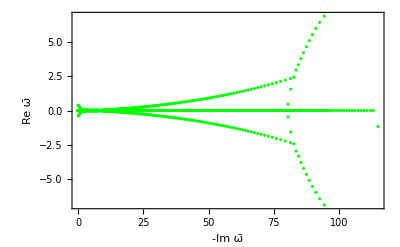

400 =n

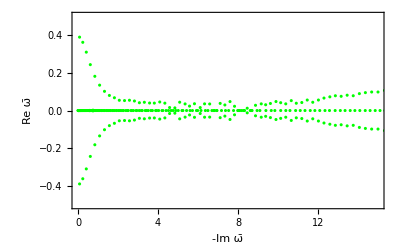

```mathematica
l400=Length[R400]-1;
d=(l400+1)/2
f400=ListPlot[
Table[{Re[R400[[k]][[2]]],Im[R400[[k]][[2]]]},{k,1,l400}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Green]
Print[d"=n"]
h400=Show[f400,PlotRange ->  {{0,15},{-1/2,1/2}},Axes->True]
```

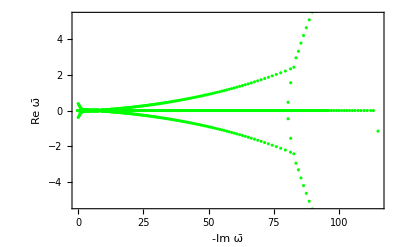

```mathematica
Show[f400,PlotRange ->  {-5.3,5.3},Axes->True]
```

```mathematica
R300=raices[300]
```

ω==0.0106586||ω==0.011268||ω==0.0210991||ω==0.0263935||ω==0.034182||ω==0.0469921||ω==0.0499998||ω==0.0685852||ω==0.0731909||ω==0.0899893||ω==0.10511||ω==0.114248||ω==0.141366||ω==0.142988||ω==0.171519||ω==0.186952||ω==0.204674||ω==0.237384||ω==0.240966||ω==0.280349||ω==0.294759||ω==0.323076||ω==0.359325||ω==0.369191||ω==0.418656||ω==0.431774||ω==0.471797||ω==0.512413||ω==0.528628||ω==0.588928||ω==0.602373||ω==0.653413||ω==0.701367||ω==0.72183||ω==0.794056||ω==0.811566||ω==0.870732||ω==0.932378||ω==0.951647||ω==1.03691||ω==1.06612||ω==1.12676||ω==1.21127||ω==1.22087||ω==1.32107||ω==1.37711||ω==1.42509||ω==1.64959||ω==1.73226||ω==1.76538||ω==1.89295||ω==1.94703||ω==2.0229||ω==2.14461||ω==2.19084||ω==2.31628||ω==2.39567||ω==2.4681||ω==2.63283||ω==2.66||ω==2.77258||ω==2.92643||ω==2.96084||ω==3.1265||ω==3.22681||ω==3.30257||ω==3.46628||ω==3.54167||ω==3.71923||ω==3.9076||ω==3.94419||ω==4.13693||ω==4.26282||ω==4.42492||ω==4.64245||ω==4.69145||ω==4.86236||ω==5.09942||ω==5.22237||ω==5.43842||ω==5.53984||ω==5.56766||ω==5.66978||ω==5.70809||ω==5.94886||ω==6.15598||ω==6.31463||ω==6.61723||ω==6.79515||ω==7.0273||ω==7.33658||ω==7.52942||ω==7.78325||ω==8.10408||ω==8.30754||ω==8.5824||ω==8.90511||ω==9.09599||ω==9.36314||ω==9.60777||ω==9.73047||ω==9.76202||ω==9.82226||ω==10.0926||ω==10.3223||ω==10.5973||ω==10.8753||ω==11.0932||ω==11.3435||ω==11.592||ω==11.8503||ω==12.1141||ω==12.3373||ω==12.5961||ω==12.8635||ω==13.1002||ω==13.352||ω==13.5968||ω==13.8608||ω==14.1001||ω==14.3465||ω==14.6147||ω==14.8464||ω==15.1071||ω==15.3586||ω==15.6002||ω==15.86||ω==16.1051||ω==16.3555||ω==16.6069||ω==16.8571||ω==17.1051||ω==17.3586||ω==17.6063||ω==17.8573||ω==18.109||ω==18.3553||ω==18.6104||ω==18.8556||ω==19.1102||ω==19.3576||ω==19.6091||ω==19.8593||ω==20.1085||ω==20.36||ω==20.6087||ω==20.8601||ω==21.1095||ω==21.3599||ω==21.6104||ω==21.8598||ω==22.1109||ω==22.3601||ω==22.611||ω==22.8606||ω==23.1109||ω==23.3611||ω==23.6109||ω==23.8616||ω==24.111||ω==24.3618||ω==24.6114||ω==24.8618||ω==25.1119||ω==25.3618||ω==25.6123||ω==25.8619||ω==26.1124||ω==26.3623||ω==26.6124||ω==26.8628||ω==27.1123||ω==27.3632||ω==27.6125||ω==27.8631||ω==28.1131||ω==28.3627||ω==28.6139||ω==28.8624||ω==29.1142||ω==29.3628||ω==29.6139||ω==29.8636||ω==30.1135||ω==30.3639||ω==30.6139||ω==30.8636||ω==31.1145||ω==31.3636||ω==31.6144||ω==31.8642||ω==32.114||ω==32.3646||ω==32.6143||ω==32.8644||ω==33.1148||ω==33.3644||ω==33.6146||ω==33.865||ω==34.1145||ω==34.365||ω==34.615||ω==34.8648||ω==35.115||ω==35.3653||ω==35.6149||ω==35.8654||ω==36.1153||ω==36.3652||ω==36.6153||ω==36.8656||ω==37.1152||ω==37.3656||ω==37.6157||ω==37.8656||ω==38.1156||ω==38.3659||ω==38.6157||ω==38.8657||ω==39.116||ω==39.366||ω==39.6158||ω==39.8661||ω==40.1162||ω==40.366||ω==40.6161||ω==40.8663||ω==41.1163||ω==41.3661||ω==41.6164||ω==41.8664||ω==42.1164||ω==42.3663||ω==42.6166||ω==42.8665||ω==43.1165||ω==43.3665||ω==43.6168||ω==43.8667||ω==44.1167||ω==44.3667||ω==44.6169||ω==44.8668||ω==45.1168||ω==45.3669||ω==45.6171||ω==45.867||ω==46.117||ω==46.367||ω==46.6172||ω==46.8672||ω==47.1171||ω==47.3672||ω==47.6172||ω==47.8674||ω==48.1172||ω==48.3673||ω==48.6173||ω==48.8675||ω==49.1174||ω==49.3674||ω==49.6174||ω==49.8675||ω==50.1176||ω==50.3676||ω==50.6176||ω==50.8676||ω==51.1177||ω==51.3677||ω==51.6178||ω==51.8677||ω==52.1177||ω==52.3679||ω==52.6179||ω==52.8679||ω==53.1178||ω==53.3679||ω==53.6179||ω==53.8681||ω==54.118||ω==54.368||ω==54.618||ω==54.868||ω==55.1182||ω==55.3682||ω==55.6182||ω==55.8681||ω==56.1181||ω==56.3682||ω==56.6183||ω==56.8684||ω==57.1183||ω==57.3684||ω==57.6183||ω==57.8683||ω==58.1183||ω==58.3682||ω==58.6184||ω==58.8678||ω==59.1187||ω==59.377||ω==59.6304||ω==59.8854||ω==60.4925||ω==60.8344||ω==61.0669||ω==61.4227||ω==61.8277||ω==62.0935||ω==62.413||ω==62.8343||ω==63.1421||ω==63.4268||ω==63.8556||ω==64.2||ω==64.4713||ω==64.9136||ω==65.2699||ω==65.5457||ω==65.9995||ω==66.3492||ω==66.6479||ω==67.133||ω==67.4446||ω==67.8229||ω==68.3199||ω==68.5769||ω==69.0904||ω==69.4674||ω==69.8395||ω==70.3829||ω==70.6497||ω==71.3061||ω==71.5779||ω==72.4473||ω==73.4008||ω==74.3675||ω==75.3465||ω==76.3414||ω==77.3563||ω==78.3958||ω==79.4649||ω==80.5688||ω==81.7135||ω==82.9132||ω==84.0905||ω==0.078206-0.388691 ⅈ||ω==0.078206+0.388691 ⅈ||ω==0.23905-0.361323 ⅈ||ω==0.23905+0.361323 ⅈ||ω==0.414656-0.309183 ⅈ||ω==0.414656+0.309183 ⅈ||ω==0.615588-0.243026 ⅈ||ω==0.615588+0.243026 ⅈ||ω==0.841469-0.181321 ⅈ||ω==0.841469+0.181321 ⅈ||ω==1.08055-0.134344 ⅈ||ω==1.08055+0.134344 ⅈ||ω==1.32352-0.102129 ⅈ||ω==1.32352+0.102129 ⅈ||ω==1.53858-0.00788788 ⅈ||ω==1.53858+0.00788788 ⅈ||ω==1.57276-0.0785366 ⅈ||ω==1.57276+0.0785366 ⅈ||ω==1.82146-0.0701615 ⅈ||ω==1.82146+0.0701615 ⅈ||ω==2.06837-0.0613309 ⅈ||ω==2.06837+0.0613309 ⅈ||ω==2.31246-0.0484211 ⅈ||ω==2.31246+0.0484211 ⅈ||ω==2.55927-0.0531371 ⅈ||ω==2.55927+0.0531371 ⅈ||ω==2.82096-0.0515863 ⅈ||ω==2.82096+0.0515863 ⅈ||ω==3.07436-0.049793 ⅈ||ω==3.07436+0.049793 ⅈ||ω==3.34374-0.0307847 ⅈ||ω==3.34374+0.0307847 ⅈ||ω==3.59737-0.0408212 ⅈ||ω==3.59737+0.0408212 ⅈ||ω==3.81124-0.0387598 ⅈ||ω==3.81124+0.0387598 ⅈ||ω==4.08174-0.0447405 ⅈ||ω==4.08174+0.0447405 ⅈ||ω==4.33069-0.0288426 ⅈ||ω==4.33069+0.0288426 ⅈ||ω==4.55391-0.0228003 ⅈ||ω==4.55391+0.0228003 ⅈ||ω==4.84975-0.0292098 ⅈ||ω==4.84975+0.0292098 ⅈ||ω==5.06377-0.0270143 ⅈ||ω==5.06377+0.0270143 ⅈ||ω==5.32612-0.0391204 ⅈ||ω==5.32612+0.0391204 ⅈ||ω==5.85794-0.0402161 ⅈ||ω==5.85794+0.0402161 ⅈ||ω==6.09904-0.027181 ⅈ||ω==6.09904+0.027181 ⅈ||ω==6.36949-0.0434685 ⅈ||ω==6.36949+0.0434685 ⅈ||ω==6.58111-0.0387885 ⅈ||ω==6.58111+0.0387885 ⅈ||ω==6.85062-0.0386249 ⅈ||ω==6.85062+0.0386249 ⅈ||ω==7.09817-0.0506996 ⅈ||ω==7.09817+0.0506996 ⅈ||ω==7.31989-0.0296474 ⅈ||ω==7.31989+0.0296474 ⅈ||ω==7.5949-0.0431929 ⅈ||ω==7.5949+0.0431929 ⅈ||ω==7.84697-0.0514219 ⅈ||ω==7.84697+0.0514219 ⅈ||ω==8.07645-0.0414464 ⅈ||ω==8.07645+0.0414464 ⅈ||ω==8.36001-0.0493663 ⅈ||ω==8.36001+0.0493663 ⅈ||ω==8.61784-0.051699 ⅈ||ω==8.61784+0.051699 ⅈ||ω==8.86027-0.0478706 ⅈ||ω==8.86027+0.0478706 ⅈ||ω==9.16431-0.0460334 ⅈ||ω==9.16431+0.0460334 ⅈ||ω==9.44359-0.0343802 ⅈ||ω==9.44359+0.0343802 ⅈ||ω==10.0385-0.0533107 ⅈ||ω==10.0385+0.0533107 ⅈ||ω==10.3458-0.0619356 ⅈ||ω==10.3458+0.0619356 ⅈ||ω==10.6386-0.0693306 ⅈ||ω==10.6386+0.0693306 ⅈ||ω==10.9415-0.0502151 ⅈ||ω==10.9415+0.0502151 ⅈ||ω==11.2677-0.0682773 ⅈ||ω==11.2677+0.0682773 ⅈ||ω==11.5893-0.0771889 ⅈ||ω==11.5893+0.0771889 ⅈ||ω==11.9109-0.084125 ⅈ||ω==11.9109+0.084125 ⅈ||ω==12.2451-0.0746241 ⅈ||ω==12.2451+0.0746241 ⅈ||ω==12.5838-0.0930146 ⅈ||ω==12.5838+0.0930146 ⅈ||ω==12.9209-0.0929903 ⅈ||ω==12.9209+0.0929903 ⅈ||ω==13.2738-0.100676 ⅈ||ω==13.2738+0.100676 ⅈ||ω==13.6295-0.108661 ⅈ||ω==13.6295+0.108661 ⅈ||ω==13.9878-0.109286 ⅈ||ω==13.9878+0.109286 ⅈ||ω==14.3571-0.119942 ⅈ||ω==14.3571+0.119942 ⅈ||ω==14.7269-0.120382 ⅈ||ω==14.7269+0.120382 ⅈ||ω==15.1056-0.131762 ⅈ||ω==15.1056+0.131762 ⅈ||ω==15.4914-0.135417 ⅈ||ω==15.4914+0.135417 ⅈ||ω==15.8812-0.143826 ⅈ||ω==15.8812+0.143826 ⅈ||ω==16.28-0.150576 ⅈ||ω==16.28+0.150576 ⅈ||ω==16.6838-0.157717 ⅈ||ω==16.6838+0.157717 ⅈ||ω==17.095-0.16509 ⅈ||ω==17.095+0.16509 ⅈ||ω==17.5122-0.172308 ⅈ||ω==17.5122+0.172308 ⅈ||ω==17.9364-0.180616 ⅈ||ω==17.9364+0.180616 ⅈ||ω==18.3681-0.188644 ⅈ||ω==18.3681+0.188644 ⅈ||ω==18.8063-0.196581 ⅈ||ω==18.8063+0.196581 ⅈ||ω==19.2515-0.205258 ⅈ||ω==19.2515+0.205258 ⅈ||ω==19.7044-0.21439 ⅈ||ω==19.7044+0.21439 ⅈ||ω==20.1648-0.223633 ⅈ||ω==20.1648+0.223633 ⅈ||ω==20.6328-0.233069 ⅈ||ω==20.6328+0.233069 ⅈ||ω==21.1085-0.242853 ⅈ||ω==21.1085+0.242853 ⅈ||ω==21.5922-0.253015 ⅈ||ω==21.5922+0.253015 ⅈ||ω==22.0839-0.263526 ⅈ||ω==22.0839+0.263526 ⅈ||ω==22.584-0.274376 ⅈ||ω==22.584+0.274376 ⅈ||ω==23.0925-0.285585 ⅈ||ω==23.0925+0.285585 ⅈ||ω==23.6097-0.297178 ⅈ||ω==23.6097+0.297178 ⅈ||ω==24.1358-0.309174 ⅈ||ω==24.1358+0.309174 ⅈ||ω==24.6709-0.321585 ⅈ||ω==24.6709+0.321585 ⅈ||ω==25.2153-0.334427 ⅈ||ω==25.2153+0.334427 ⅈ||ω==25.7693-0.347726 ⅈ||ω==25.7693+0.347726 ⅈ||ω==26.3331-0.361502 ⅈ||ω==26.3331+0.361502 ⅈ||ω==26.907-0.375767 ⅈ||ω==26.907+0.375767 ⅈ||ω==27.4912-0.390549 ⅈ||ω==27.4912+0.390549 ⅈ||ω==28.086-0.405875 ⅈ||ω==28.086+0.405875 ⅈ||ω==28.6919-0.42176 ⅈ||ω==28.6919+0.42176 ⅈ||ω==29.3091-0.438246 ⅈ||ω==29.3091+0.438246 ⅈ||ω==29.938-0.455358 ⅈ||ω==29.938+0.455358 ⅈ||ω==30.5789-0.47312 ⅈ||ω==30.5789+0.47312 ⅈ||ω==31.2324-0.491569 ⅈ||ω==31.2324+0.491569 ⅈ||ω==31.8989-0.510747 ⅈ||ω==31.8989+0.510747 ⅈ||ω==32.5788-0.530691 ⅈ||ω==32.5788+0.530691 ⅈ||ω==33.2726-0.551444 ⅈ||ω==33.2726+0.551444 ⅈ||ω==33.981-0.573053 ⅈ||ω==33.981+0.573053 ⅈ||ω==34.7046-0.59557 ⅈ||ω==34.7046+0.59557 ⅈ||ω==35.444-0.619051 ⅈ||ω==35.444+0.619051 ⅈ||ω==36.2-0.643558 ⅈ||ω==36.2+0.643558 ⅈ||ω==36.9733-0.669158 ⅈ||ω==36.9733+0.669158 ⅈ||ω==37.7649-0.695926 ⅈ||ω==37.7649+0.695926 ⅈ||ω==38.5756-0.723943 ⅈ||ω==38.5756+0.723943 ⅈ||ω==39.4067-0.753302 ⅈ||ω==39.4067+0.753302 ⅈ||ω==40.2592-0.784104 ⅈ||ω==40.2592+0.784104 ⅈ||ω==41.1346-0.816465 ⅈ||ω==41.1346+0.816465 ⅈ||ω==42.0343-0.850512 ⅈ||ω==42.0343+0.850512 ⅈ||ω==42.96-0.886391 ⅈ||ω==42.96+0.886391 ⅈ||ω==43.9137-0.924269 ⅈ||ω==43.9137+0.924269 ⅈ||ω==44.8976-0.964336 ⅈ||ω==44.8976+0.964336 ⅈ||ω==45.9144-1.00681 ⅈ||ω==45.9144+1.00681 ⅈ||ω==46.967-1.05195 ⅈ||ω==46.967+1.05195 ⅈ||ω==48.0591-1.10007 ⅈ||ω==48.0591+1.10007 ⅈ||ω==49.1949-1.1515 ⅈ||ω==49.1949+1.1515 ⅈ||ω==50.3798-1.20671 ⅈ||ω==50.3798+1.20671 ⅈ||ω==51.6204-1.26621 ⅈ||ω==51.6204+1.26621 ⅈ||ω==52.9248-1.33068 ⅈ||ω==52.9248+1.33068 ⅈ||ω==54.3041-1.40098 ⅈ||ω==54.3041+1.40098 ⅈ||ω==55.7728-1.47825 ⅈ||ω==55.7728+1.47825 ⅈ||ω==57.3517-1.56406 ⅈ||ω==57.3517+1.56406 ⅈ||ω==59.0718-1.6608 ⅈ||ω==59.0718+1.6608 ⅈ||ω==60.1581-0.0824666 ⅈ||ω==60.1581+0.0824666 ⅈ||ω==61.0108-1.77582 ⅈ||ω==61.0108+1.77582 ⅈ||ω==61.1514-1.08378 ⅈ||ω==61.1514+1.08378 ⅈ||ω==62.3494-1.91715 ⅈ||ω==62.3494+1.91715 ⅈ||ω==63.1515-2.43355 ⅈ||ω==63.1515+2.43355 ⅈ||ω==64.1301-2.80261 ⅈ||ω==64.1301+2.80261 ⅈ||ω==65.1562-3.26824 ⅈ||ω==65.1562+3.26824 ⅈ||ω==66.2237-3.69816 ⅈ||ω==66.2237+3.69816 ⅈ||ω==67.426-4.13113 ⅈ||ω==67.426+4.13113 ⅈ||ω==68.7704-4.59834 ⅈ||ω==68.7704+4.59834 ⅈ||ω==70.3715-5.05472 ⅈ||ω==70.3715+5.05472 ⅈ||ω==85.7708-0.670303 ⅈ||ω==85.7708+0.670303 ⅈ

300

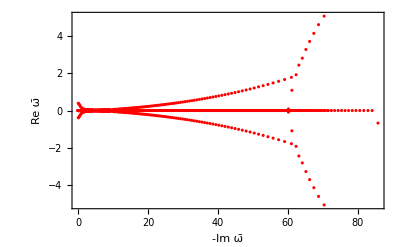

300 =n

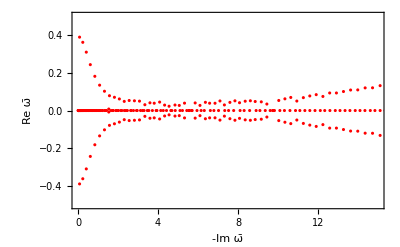

```mathematica
l300=Length[R300]-1;
d=(l300+1)/2
f300=ListPlot[
Table[{Re[R300[[k]][[2]]],Im[R300[[k]][[2]]]},{k,1,l300}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Red]
Print[d"=n"]
h300=Show[f300,PlotRange ->  {{0,15},{-1/2,1/2}},Axes->True]
```

```mathematica
R200=raices[200]
```

ω==0.0159698||ω==0.0168775||ω==0.0316292||ω==0.0395697||ω==0.0512795||ω==0.0705759||ω==0.0750911||ω==0.103138||ω==0.110252||ω==0.135578||ω==0.158988||ω==0.172525||ω==0.21401||ω==0.217554||ω==0.260524||ω==0.286453||ω==0.312023||ω==0.366566||ω==0.369194||ω==0.430933||ω==0.460395||ω==0.498929||ω==0.568216||ω==0.572762||ω==0.653148||ω==0.691675||ω==0.739692||ω==0.93431||ω==0.996079||ω==1.04051||ω==1.16108||ω==1.18158||ω==1.28072||ω==1.55719||ω==1.64776||ω==1.70764||ω==1.86725||ω==1.927||ω==2.04201||ω==2.18183||ω==2.24271||ω==2.43184||ω==2.5305||ω==2.55864||ω==2.61422||ω==2.62774||ω==2.85103||ω==2.9588||ω==3.13007||ω==3.61416||ω==3.84835||ω==3.97667||ω==4.22382||ω==4.46119||ω==4.52721||ω==4.59626||ω==4.66274||ω==4.94181||ω==5.03645||ω==5.06565||ω==5.19793||ω==5.26636||ω==5.34729||ω==5.42852||ω==5.73409||ω==6.00683||ω==6.2675||ω==6.63538||ω==6.92585||ω==7.09251||ω==7.35155||ω==7.48308||ω==7.84394||ω==8.18752||ω==8.33571||ω==8.591||ω==8.82384||ω==9.11096||ω==9.34006||ω==9.5653||ω==9.8741||ω==10.0801||ω==10.3507||ω==10.6061||ω==10.8345||ω==11.1141||ω==11.3461||ω==11.5997||ω==11.8529||ω==12.0974||ω==12.3554||ω==12.5995||ω==12.8546||ω==13.1015||ω==13.353||ω==13.6037||ω==13.8512||ω==14.1066||ω==14.3493||ω==14.6097||ω==14.8477||ω==15.112||ω==15.347||ω==15.6129||ω==15.8474||ω==16.1123||ω==16.3493||ω==16.6107||ω==16.8526||ω==17.1085||ω==17.3569||ω==17.606||ω==17.8605||ω==18.104||ω==18.3618||ω==18.6041||ω==18.8607||ω==19.1069||ω==19.3589||ω==19.6093||ω==19.8586||ω==20.1087||ω==20.3612||ω==20.6069||ω==20.8625||ω==21.1075||ω==21.3606||ω==21.6106||ω==21.8593||ω==22.1105||ω==22.3616||ω==22.6089||ω==22.862||ω==23.1108||ω==23.3602||ω==23.6119||ω==23.8616||ω==24.1102||ω==24.3625||ω==24.6117||ω==24.8609||ω==25.1122||ω==25.3627||ω==25.6109||ω==25.8625||ω==26.1128||ω==26.362||ω==26.6118||ω==26.8636||ω==27.1123||ω==27.3623||ω==27.6128||ω==27.864||ω==28.1121||ω==28.3631||ω==28.6133||ω==28.864||ω==29.1123||ω==29.3636||ω==29.6137||ω==29.8642||ω==30.1128||ω==30.3638||ω==30.6142||ω==30.8643||ω==31.1134||ω==31.3637||ω==31.6146||ω==31.8645||ω==32.1142||ω==32.3636||ω==32.6148||ω==32.8647||ω==33.115||ω==33.3638||ω==33.6145||ω==33.8648||ω==34.1154||ω==34.3649||ω==34.6143||ω==34.8648||ω==35.115||ω==35.3659||ω==35.6151||ω==35.8651||ω==36.1146||ω==36.3653||ω==36.6158||ω==36.8658||ω==37.1157||ω==37.3648||ω==37.6153||ω==37.8653||ω==38.1163||ω==38.3663||ω==38.6163||ω==38.8666||ω==39.1147||ω==39.3645||ω==39.6111||ω==39.8383||ω==40.1017||ω==40.394||ω==40.6422||ω==41.0115||ω==41.4251||ω==41.6828||ω==42.0229||ω==42.4492||ω==42.7329||ω==43.0468||ω==43.4856||ω==43.799||ω==44.128||ω==44.6159||ω==44.8941||ω==45.3166||ω==45.7755||ω==46.0404||ω==46.5541||ω==46.8998||ω==47.3357||ω==47.8747||ω==48.7953||ω==49.7443||ω==50.715||ω==51.715||ω==52.7531||ω==53.8404||ω==54.9741||ω==56.4756||ω==56.7975||ω==0.078206-0.388691 ⅈ||ω==0.078206+0.388691 ⅈ||ω==0.23905-0.361323 ⅈ||ω==0.23905+0.361323 ⅈ||ω==0.414656-0.309183 ⅈ||ω==0.414656+0.309183 ⅈ||ω==0.615588-0.243027 ⅈ||ω==0.615588+0.243027 ⅈ||ω==0.833725-0.00491623 ⅈ||ω==0.833725+0.00491623 ⅈ||ω==0.841483-0.181301 ⅈ||ω==0.841483+0.181301 ⅈ||ω==1.08055-0.134874 ⅈ||ω==1.08055+0.134874 ⅈ||ω==1.32261-0.10326 ⅈ||ω==1.32261+0.10326 ⅈ||ω==1.40914-0.0034853 ⅈ||ω==1.40914+0.0034853 ⅈ||ω==1.56605-0.0815722 ⅈ||ω==1.56605+0.0815722 ⅈ||ω==1.81289-0.0722052 ⅈ||ω==1.81289+0.0722052 ⅈ||ω==2.06943-0.0594772 ⅈ||ω==2.06943+0.0594772 ⅈ||ω==2.32547-0.0640399 ⅈ||ω==2.32547+0.0640399 ⅈ||ω==2.80826-0.0502914 ⅈ||ω==2.80826+0.0502914 ⅈ||ω==3.06757-0.036082 ⅈ||ω==3.06757+0.036082 ⅈ||ω==3.28352-0.0128886 ⅈ||ω==3.28352+0.0128886 ⅈ||ω==3.39277-0.0148806 ⅈ||ω==3.39277+0.0148806 ⅈ||ω==3.58257-0.0424145 ⅈ||ω==3.58257+0.0424145 ⅈ||ω==3.80887-0.0313274 ⅈ||ω==3.80887+0.0313274 ⅈ||ω==4.07978-0.0539609 ⅈ||ω==4.07978+0.0539609 ⅈ||ω==4.31403-0.0389835 ⅈ||ω==4.31403+0.0389835 ⅈ||ω==4.80753-0.0365248 ⅈ||ω==4.80753+0.0365248 ⅈ||ω==5.56315-0.0424986 ⅈ||ω==5.56315+0.0424986 ⅈ||ω==5.81442-0.0277098 ⅈ||ω==5.81442+0.0277098 ⅈ||ω==6.07881-0.0321532 ⅈ||ω==6.07881+0.0321532 ⅈ||ω==6.35147-0.0580852 ⅈ||ω==6.35147+0.0580852 ⅈ||ω==6.59098-0.0475096 ⅈ||ω==6.59098+0.0475096 ⅈ||ω==6.86831-0.0217969 ⅈ||ω==6.86831+0.0217969 ⅈ||ω==7.2135-0.0284158 ⅈ||ω==7.2135+0.0284158 ⅈ||ω==7.57796-0.0541646 ⅈ||ω==7.57796+0.0541646 ⅈ||ω==7.85252-0.0555654 ⅈ||ω==7.85252+0.0555654 ⅈ||ω==8.14111-0.0151666 ⅈ||ω==8.14111+0.0151666 ⅈ||ω==8.52464-0.0537952 ⅈ||ω==8.52464+0.0537952 ⅈ||ω==8.87732-0.0708002 ⅈ||ω==8.87732+0.0708002 ⅈ||ω==9.22329-0.054371 ⅈ||ω==9.22329+0.054371 ⅈ||ω==9.60269-0.0808086 ⅈ||ω==9.60269+0.0808086 ⅈ||ω==9.96083-0.060298 ⅈ||ω==9.96083+0.060298 ⅈ||ω==10.3471-0.0907127 ⅈ||ω==10.3471+0.0907127 ⅈ||ω==10.7429-0.0871936 ⅈ||ω==10.7429+0.0871936 ⅈ||ω==11.1381-0.100454 ⅈ||ω==11.1381+0.100454 ⅈ||ω==11.5554-0.110586 ⅈ||ω==11.5554+0.110586 ⅈ||ω==11.9776-0.11659 ⅈ||ω==11.9776+0.11659 ⅈ||ω==12.4092-0.125764 ⅈ||ω==12.4092+0.125764 ⅈ||ω==12.8529-0.135634 ⅈ||ω==12.8529+0.135634 ⅈ||ω==13.308-0.145095 ⅈ||ω==13.308+0.145095 ⅈ||ω==13.7742-0.15448 ⅈ||ω==13.7742+0.15448 ⅈ||ω==14.2516-0.164152 ⅈ||ω==14.2516+0.164152 ⅈ||ω==14.7409-0.174486 ⅈ||ω==14.7409+0.174486 ⅈ||ω==15.2426-0.185699 ⅈ||ω==15.2426+0.185699 ⅈ||ω==15.7572-0.197829 ⅈ||ω==15.7572+0.197829 ⅈ||ω==16.2852-0.210836 ⅈ||ω==16.2852+0.210836 ⅈ||ω==16.8266-0.224526 ⅈ||ω==16.8266+0.224526 ⅈ||ω==17.3821-0.238578 ⅈ||ω==17.3821+0.238578 ⅈ||ω==17.9528-0.25303 ⅈ||ω==17.9528+0.25303 ⅈ||ω==18.5392-0.268518 ⅈ||ω==18.5392+0.268518 ⅈ||ω==19.1416-0.285016 ⅈ||ω==19.1416+0.285016 ⅈ||ω==19.7608-0.302202 ⅈ||ω==19.7608+0.302202 ⅈ||ω==20.3979-0.320319 ⅈ||ω==20.3979+0.320319 ⅈ||ω==21.0538-0.339552 ⅈ||ω==21.0538+0.339552 ⅈ||ω==21.7293-0.359994 ⅈ||ω==21.7293+0.359994 ⅈ||ω==22.4258-0.381621 ⅈ||ω==22.4258+0.381621 ⅈ||ω==23.1444-0.404637 ⅈ||ω==23.1444+0.404637 ⅈ||ω==23.8867-0.429129 ⅈ||ω==23.8867+0.429129 ⅈ||ω==24.6543-0.45526 ⅈ||ω==24.6543+0.45526 ⅈ||ω==25.4491-0.483192 ⅈ||ω==25.4491+0.483192 ⅈ||ω==26.2734-0.513133 ⅈ||ω==26.2734+0.513133 ⅈ||ω==27.1297-0.545305 ⅈ||ω==27.1297+0.545305 ⅈ||ω==28.0212-0.579988 ⅈ||ω==28.0212+0.579988 ⅈ||ω==28.9515-0.617516 ⅈ||ω==28.9515+0.617516 ⅈ||ω==29.9251-0.658291 ⅈ||ω==29.9251+0.658291 ⅈ||ω==30.9475-0.702816 ⅈ||ω==30.9475+0.702816 ⅈ||ω==32.0259-0.751725 ⅈ||ω==32.0259+0.751725 ⅈ||ω==33.1694-0.805841 ⅈ||ω==33.1694+0.805841 ⅈ||ω==34.3903-0.866266 ⅈ||ω==34.3903+0.866266 ⅈ||ω==35.7061-0.934542 ⅈ||ω==35.7061+0.934542 ⅈ||ω==37.1427-1.01295 ⅈ||ω==37.1427+1.01295 ⅈ||ω==38.7424-1.10528 ⅈ||ω==38.7424+1.10528 ⅈ||ω==40.6125-1.21219 ⅈ||ω==40.6125+1.21219 ⅈ||ω==40.8146-0.61215 ⅈ||ω==40.8146+0.61215 ⅈ||ω==42.0058-1.40367 ⅈ||ω==42.0058+1.40367 ⅈ||ω==42.8361-1.91808 ⅈ||ω==42.8361+1.91808 ⅈ||ω==43.8968-2.2755 ⅈ||ω==43.8968+2.2755 ⅈ||ω==45.1057-2.76606 ⅈ||ω==45.1057+2.76606 ⅈ||ω==46.4613-3.24932 ⅈ||ω==46.4613+3.24932 ⅈ

200

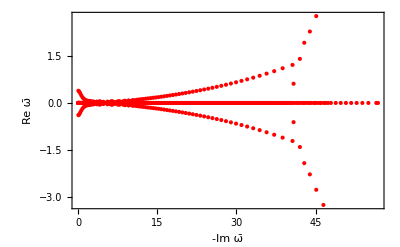

200 =n

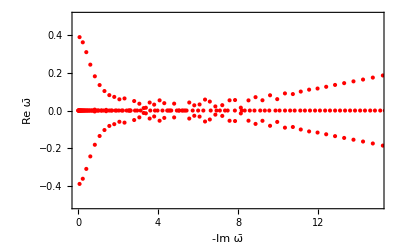

```mathematica
l200=Length[R200]-1;
d=(l200+1)/2
f200=ListPlot[
Table[{Re[R200[[k]][[2]]],Im[R200[[k]][[2]]]},{k,1,l200}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Red]
Print[d"=n"]
h200=Show[f200,PlotRange ->  {{0,15},{-1/2,1/2}},Axes->True]
```

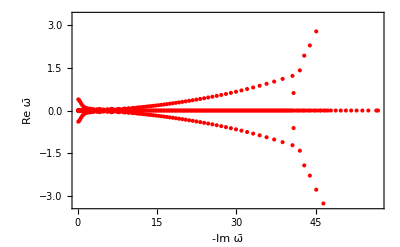

```mathematica
Show[f200,PlotRange ->{-3.3,3.3}]
```

```mathematica
f400
```

-Graphics-

```mathematica
f300
```

f300

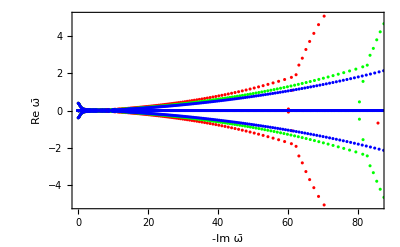

```mathematica
Show[f300,f400,f500]
```

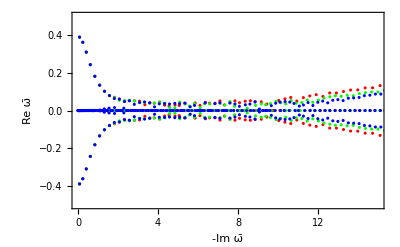

```mathematica
Show[h300,h400,h500]
```